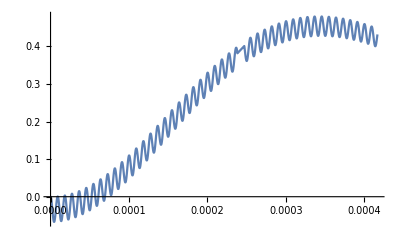

```mathematica
ClearAll["Global`*"]

uzel1= 0==iUz[t]+iR1[t];
uzel2=iR1[t]+iZ[t]==iR2[t]+iL[t]+iC1[t];
uzel3=iL[t]==iZ[t]+iR3[t]+iC2[t];

rezistor1=iR1[t]*R1==u1[t]-u2[t];
rezistor2=iR2[t]*R2== u2[t];
rezistor3=iR3[t]*R3 == u3[t];

civka = iL'[t]*L ==u2[t]-u3[t];
kond1 = iC1[t]==C1*u2'[t];
kond2 = iC2[t] == C2*u3'[t];

pp1=iL[0]==0;
pp2=u2[0]==0;
pp3=u3[0]==0;

zdroj=uZ[t]==u1[t];

rovnice = {uzel1, uzel2, uzel3, rezistor1, rezistor2, rezistor3, civka, kond1, kond2, pp1, pp2, pp3, zdroj};

nezname = {u1[t], u2[t], u3[t], iUz[t], iR1[t], iR2[t], iR3[t], iL[t],iC1[t], iC2[t]};

soucastky= {R1 -> 10*10^3, R2->22*10^3, R3-> 33*10^3, C1-> 56*10^-9, C2->47*10^-9, L->82*10^-6};

amplitudaU= 5;
frekvenceU = 1200;
perioda = 1/frekvenceU;
tmax=0.5*perioda;
uZ[t_] := amplitudaU*Sin[2*π*frekvenceU*t]/2;

amplitudaI=0.1;
frekvenceI=2400;
iZ[t_]:=amplitudaI*Sin[2*π*frekvenceI*t]/2;

Plot[uZ[t],{t,0,tmax}];

reseni = NDSolve[rovnice /. soucastky, nezname,{t,0,tmax}, StartingStepSize->10^-9,Method->{"IndexReduction"->Automatic}];

Plot[u3[t]/.reseni, {t, 0, tmax}]
```

```mathematica
R1= 10*10^3;
R2=22*10^3;
R3= 33*10^3;
uZ = 5;
Rx= (R2*R3)/(R2+R3);
Uout = uZ * Rx/(R1+Rx)
```

165/58